```mathematica
deps3=ReadList["D:\\Grofs\\dependencies3.txt",Expression];Length[deps3]
```

2436995

```mathematica
GraphSolutions2[g_,pre_, circle_]:=Block[{sols, colors},
sols=ToVars2[g,pre];
colors=Map[Sort[ToColors[#]]&,sols];
colors=Map[Map[#[[1]]->If[MemberQ[circle,#[[1]]],Lighter[#[[2]]],Darker[#[[2]]]]&,#]&, colors];
colors=Map[Map[Last[#]&,#]&,colors];
colors
]
```

```mathematica
BoldCycle[all_,cycle_]:=
Map[If[MemberQ[cycle,#],Style[#,Bold,Underlined],#]&,all]
```

```mathematica
BoldCycle[Range[10],{2,4,6}]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
Take[deps3,3]
```

{{2,3,{3,{3,2,1,5,4},{2<->4,2<->5},{{2,3,4},{2,4,5},{1,2,5}}}},{3,6,{3,{2,5,4,3,1},{1<->5,3<->5},{{1,2,5},{1,3,5},{3,4,5}}}},{3,5,{3,{1,2,3,6,5},{2<->5,2<->6},{{1,2,5},{2,5,6},{2,3,6}}}}}

```mathematica
MyGrid[g_,l_, circle_]:=Labeled[TableForm[GraphSolutions2[g,"x"<>ToString[circle[[3]]]<>"==1&&x"<>ToString[circle[[2]]]<>"==2",circle],TableSpacing->{0,0}, TableHeadings->{{},BoldCycle[Sort[VertexList[g]],circle]}], ToString[ChromaticPolynomial[g,4]/24]<>" - " <> l]
```

```mathematica
MyEdgeDelete[g_,edges_]:=Block[{result, i,e},
result=g;
For[i=1,i≤Length[edges],i++,
e=edges[[i]];
If[EdgeQ[result,e],result=EdgeDelete[result,e]];
e=e[[2]]<->e[[1]];
If[EdgeQ[result,e],result=EdgeDelete[result,e]]
];
result
]
```

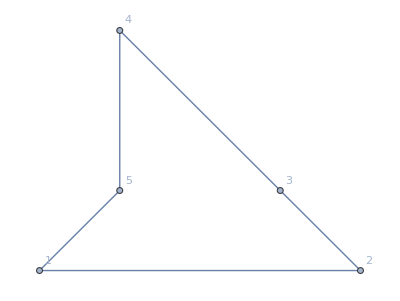
{-Graphics- | 1 | 2 | 3 | 4 | 5
 | RGBColor[1, Rational[1, 3], Rational[1, 3]] | RGBColor[Rational[1, 3], 1, Rational[1, 3]] | RGBColor[1, Rational[1, 3], Rational[1, 3]] | RGBColor[Rational[1, 3], Rational[1, 3], 1] | RGBColor[Rational[1, 3], 1, Rational[1, 3]]
 | RGBColor[1, Rational[1, 3], Rational[1, 3]] | RGBColor[Rational[1, 3], 1, Rational[1, 3]] | RGBColor[1, Rational[1, 3], Rational[1, 3]] | RGBColor[1, 1, Rational[1, 3]] | RGBColor[Rational[1, 3], 1, Rational[1, 3]]
 | RGBColor[1, Rational[1, 3], Rational[1, 3]] | RGBColor[Rational[1, 3], 1, Rational[1, 3]] | RGBColor[1, Rational[1, 3], Rational[1, 3]] | RGBColor[Rational[1, 3], 1, Rational[1, 3]] | RGBColor[Rational[1, 3], Rational[1, 3], 1]
 | RGBColor[1, Rational[1, 3], Rational[1, 3]] | RGBColor[Rational[1, 3], 1, Rational[1, 3]] | RGBColor[1, Rational[1, 3], Rational[1, 3]] | RGBColor[1, 1, Rational[1, 3]] | RGBColor[Rational[1, 3], Rational[1, 3], 1]
 | RGBColor[1, Rational[1, 3], Rational[1, 3]] | RGBColor[Rational[1, 3], 1, Rational[1, 3]] | RGBColor[1, Rational[1, 3], Rational[1, 3]] | RGBColor[Rational[1, 3], 1, Rational[1, 3]] | RGBColor[1, 1, Rational[1, 3]]
 | RGBColor[1, Rational[1, 3], Rational[1, 3]] | RGBColor[Rational[1, 3], 1, Rational[1, 3]] | RGBColor[1, Rational[1, 3], Rational[1, 3]] | RGBColor[Rational[1, 3], Rational[1, 3], 1] | RGBColor[1, 1, Rational[1, 3]]
 | RGBColor[1, Rational[1, 3], Rational[1, 3]] | RGBColor[Rational[1, 3], 1, Rational[1, 3]] | RGBColor[Rational[1, 3], Rational[1, 3], 1] | RGBColor[1, Rational[1, 3], Rational[1, 3]] | RGBColor[Rational[1, 3], 1, Rational[1, 3]]
 | RGBColor[1, Rational[1, 3], Rational[1, 3]] | RGBColor[Rational[1, 3], 1, Rational[1, 3]] | RGBColor[Rational[1, 3], Rational[1, 3], 1] | RGBColor[1, 1, Rational[1, 3]] | RGBColor[Rational[1, 3], 1, Rational[1, 3]]
 | RGBColor[1, Rational[1, 3], Rational[1, 3]] | RGBColor[Rational[1, 3], 1, Rational[1, 3]] | RGBColor[Rational[1, 3], Rational[1, 3], 1] | RGBColor[1, Rational[1, 3], Rational[1, 3]] | RGBColor[Rational[1, 3], Rational[1, 3], 1]
 | RGBColor[1, Rational[1, 3], Rational[1, 3]] | RGBColor[Rational[1, 3], 1, Rational[1, 3]] | RGBColor[Rational[1, 3], Rational[1, 3], 1] | RGBColor[Rational[1, 3], 1, Rational[1, 3]] | RGBColor[Rational[1, 3], Rational[1, 3], 1]
 | RGBColor[1, Rational[1, 3], Rational[1, 3]] | RGBColor[Rational[1, 3], 1, Rational[1, 3]] | RGBColor[Rational[1, 3], Rational[1, 3], 1] | RGBColor[1, 1, Rational[1, 3]] | RGBColor[Rational[1, 3], Rational[1, 3], 1]
 | RGBColor[1, Rational[1, 3], Rational[1, 3]] | RGBColor[Rational[1, 3], 1, Rational[1, 3]] | RGBColor[Rational[1, 3], Rational[1, 3], 1] | RGBColor[1, Rational[1, 3], Rational[1, 3]] | RGBColor[1, 1, Rational[1, 3]]
 | RGBColor[1, Rational[1, 3], Rational[1, 3]] | RGBColor[Rational[1, 3], 1, Rational[1, 3]] | RGBColor[Rational[1, 3], Rational[1, 3], 1] | RGBColor[Rational[1, 3], 1, Rational[1, 3]] | RGBColor[1, 1, Rational[1, 3]]
 | RGBColor[1, Rational[1, 3], Rational[1, 3]] | RGBColor[Rational[1, 3], 1, Rational[1, 3]] | RGBColor[1, 1, Rational[1, 3]] | RGBColor[1, Rational[1, 3], Rational[1, 3]] | RGBColor[Rational[1, 3], 1, Rational[1, 3]]
 | RGBColor[1, Rational[1, 3], Rational[1, 3]] | RGBColor[Rational[1, 3], 1, Rational[1, 3]] | RGBColor[1, 1, Rational[1, 3]] | RGBColor[Rational[1, 3], Rational[1, 3], 1] | RGBColor[Rational[1, 3], 1, Rational[1, 3]]
 | RGBColor[1, Rational[1, 3], Rational[1, 3]] | RGBColor[Rational[1, 3], 1, Rational[1, 3]] | RGBColor[1, 1, Rational[1, 3]] | RGBColor[1, Rational[1, 3], Rational[1, 3]] | RGBColor[Rational[1, 3], Rational[1, 3], 1]
 | RGBColor[1, Rational[1, 3], Rational[1, 3]] | RGBColor[Rational[1, 3], 1, Rational[1, 3]] | RGBColor[1, 1, Rational[1, 3]] | RGBColor[Rational[1, 3], 1, Rational[1, 3]] | RGBColor[Rational[1, 3], Rational[1, 3], 1]
 | RGBColor[1, Rational[1, 3], Rational[1, 3]] | RGBColor[Rational[1, 3], 1, Rational[1, 3]] | RGBColor[1, 1, Rational[1, 3]] | RGBColor[1, Rational[1, 3], Rational[1, 3]] | RGBColor[1, 1, Rational[1, 3]]
 | RGBColor[1, Rational[1, 3], Rational[1, 3]] | RGBColor[Rational[1, 3], 1, Rational[1, 3]] | RGBColor[1, 1, Rational[1, 3]] | RGBColor[Rational[1, 3], 1, Rational[1, 3]] | RGBColor[1, 1, Rational[1, 3]]
 | RGBColor[1, Rational[1, 3], Rational[1, 3]] | RGBColor[Rational[1, 3], 1, Rational[1, 3]] | RGBColor[1, 1, Rational[1, 3]] | RGBColor[Rational[1, 3], Rational[1, 3], 1] | RGBColor[1, 1, Rational[1, 3]]10 - empty | 1 | 2 | 3 | 4 | 5
 | RGBColor[1, Rational[1, 3], Rational[1, 3]] | RGBColor[Rational[1, 3], 1, Rational[1, 3]] | RGBColor[Rational[1, 3], Rational[1, 3], 1] | RGBColor[1, Rational[1, 3], Rational[1, 3]] | RGBColor[Rational[1, 3], 1, Rational[1, 3]]
 | RGBColor[1, Rational[1, 3], Rational[1, 3]] | RGBColor[Rational[1, 3], 1, Rational[1, 3]] | RGBColor[Rational[1, 3], Rational[1, 3], 1] | RGBColor[1, 1, Rational[1, 3]] | RGBColor[Rational[1, 3], 1, Rational[1, 3]]
 | RGBColor[1, Rational[1, 3], Rational[1, 3]] | RGBColor[Rational[1, 3], 1, Rational[1, 3]] | RGBColor[Rational[1, 3], Rational[1, 3], 1] | RGBColor[1, Rational[1, 3], Rational[1, 3]] | RGBColor[1, 1, Rational[1, 3]]
 | RGBColor[1, Rational[1, 3], Rational[1, 3]] | RGBColor[Rational[1, 3], 1, Rational[1, 3]] | RGBColor[Rational[1, 3], Rational[1, 3], 1] | RGBColor[Rational[1, 3], 1, Rational[1, 3]] | RGBColor[1, 1, Rational[1, 3]]
 | RGBColor[1, Rational[1, 3], Rational[1, 3]] | RGBColor[Rational[1, 3], 1, Rational[1, 3]] | RGBColor[1, 1, Rational[1, 3]] | RGBColor[1, Rational[1, 3], Rational[1, 3]] | RGBColor[Rational[1, 3], 1, Rational[1, 3]]
 | RGBColor[1, Rational[1, 3], Rational[1, 3]] | RGBColor[Rational[1, 3], 1, Rational[1, 3]] | RGBColor[1, 1, Rational[1, 3]] | RGBColor[Rational[1, 3], Rational[1, 3], 1] | RGBColor[Rational[1, 3], 1, Rational[1, 3]]
 | RGBColor[1, Rational[1, 3], Rational[1, 3]] | RGBColor[Rational[1, 3], 1, Rational[1, 3]] | RGBColor[1, 1, Rational[1, 3]] | RGBColor[1, Rational[1, 3], Rational[1, 3]] | RGBColor[Rational[1, 3], Rational[1, 3], 1]
 | RGBColor[1, Rational[1, 3], Rational[1, 3]] | RGBColor[Rational[1, 3], 1, Rational[1, 3]] | RGBColor[1, 1, Rational[1, 3]] | RGBColor[Rational[1, 3], 1, Rational[1, 3]] | RGBColor[Rational[1, 3], Rational[1, 3], 1]4 - A | 1 | 2 | 3 | 4 | 5
 | RGBColor[1, Rational[1, 3], Rational[1, 3]] | RGBColor[Rational[1, 3], 1, Rational[1, 3]] | RGBColor[1, Rational[1, 3], Rational[1, 3]] | RGBColor[1, 1, Rational[1, 3]] | RGBColor[Rational[1, 3], Rational[1, 3], 1]
 | RGBColor[1, Rational[1, 3], Rational[1, 3]] | RGBColor[Rational[1, 3], 1, Rational[1, 3]] | RGBColor[1, Rational[1, 3], Rational[1, 3]] | RGBColor[Rational[1, 3], Rational[1, 3], 1] | RGBColor[1, 1, Rational[1, 3]]
 | RGBColor[1, Rational[1, 3], Rational[1, 3]] | RGBColor[Rational[1, 3], 1, Rational[1, 3]] | RGBColor[Rational[1, 3], Rational[1, 3], 1] | RGBColor[1, Rational[1, 3], Rational[1, 3]] | RGBColor[Rational[1, 3], Rational[1, 3], 1]
 | RGBColor[1, Rational[1, 3], Rational[1, 3]] | RGBColor[Rational[1, 3], 1, Rational[1, 3]] | RGBColor[Rational[1, 3], Rational[1, 3], 1] | RGBColor[1, 1, Rational[1, 3]] | RGBColor[Rational[1, 3], Rational[1, 3], 1]
 | RGBColor[1, Rational[1, 3], Rational[1, 3]] | RGBColor[Rational[1, 3], 1, Rational[1, 3]] | RGBColor[Rational[1, 3], Rational[1, 3], 1] | RGBColor[1, Rational[1, 3], Rational[1, 3]] | RGBColor[1, 1, Rational[1, 3]]
 | RGBColor[1, Rational[1, 3], Rational[1, 3]] | RGBColor[Rational[1, 3], 1, Rational[1, 3]] | RGBColor[1, 1, Rational[1, 3]] | RGBColor[1, Rational[1, 3], Rational[1, 3]] | RGBColor[Rational[1, 3], Rational[1, 3], 1]
 | RGBColor[1, Rational[1, 3], Rational[1, 3]] | RGBColor[Rational[1, 3], 1, Rational[1, 3]] | RGBColor[1, 1, Rational[1, 3]] | RGBColor[1, Rational[1, 3], Rational[1, 3]] | RGBColor[1, 1, Rational[1, 3]]
 | RGBColor[1, Rational[1, 3], Rational[1, 3]] | RGBColor[Rational[1, 3], 1, Rational[1, 3]] | RGBColor[1, 1, Rational[1, 3]] | RGBColor[Rational[1, 3], Rational[1, 3], 1] | RGBColor[1, 1, Rational[1, 3]]4 - B | 1 | 2 | 3 | 4 | 5
 | RGBColor[1, Rational[1, 3], Rational[1, 3]] | RGBColor[Rational[1, 3], 1, Rational[1, 3]] | RGBColor[1, Rational[1, 3], Rational[1, 3]] | RGBColor[Rational[1, 3], Rational[1, 3], 1] | RGBColor[Rational[1, 3], 1, Rational[1, 3]]
 | RGBColor[1, Rational[1, 3], Rational[1, 3]] | RGBColor[Rational[1, 3], 1, Rational[1, 3]] | RGBColor[1, Rational[1, 3], Rational[1, 3]] | RGBColor[1, 1, Rational[1, 3]] | RGBColor[Rational[1, 3], 1, Rational[1, 3]]
 | RGBColor[1, Rational[1, 3], Rational[1, 3]] | RGBColor[Rational[1, 3], 1, Rational[1, 3]] | RGBColor[1, Rational[1, 3], Rational[1, 3]] | RGBColor[Rational[1, 3], 1, Rational[1, 3]] | RGBColor[Rational[1, 3], Rational[1, 3], 1]
 | RGBColor[1, Rational[1, 3], Rational[1, 3]] | RGBColor[Rational[1, 3], 1, Rational[1, 3]] | RGBColor[1, Rational[1, 3], Rational[1, 3]] | RGBColor[1, 1, Rational[1, 3]] | RGBColor[Rational[1, 3], Rational[1, 3], 1]
 | RGBColor[1, Rational[1, 3], Rational[1, 3]] | RGBColor[Rational[1, 3], 1, Rational[1, 3]] | RGBColor[1, Rational[1, 3], Rational[1, 3]] | RGBColor[Rational[1, 3], 1, Rational[1, 3]] | RGBColor[1, 1, Rational[1, 3]]
 | RGBColor[1, Rational[1, 3], Rational[1, 3]] | RGBColor[Rational[1, 3], 1, Rational[1, 3]] | RGBColor[1, Rational[1, 3], Rational[1, 3]] | RGBColor[Rational[1, 3], Rational[1, 3], 1] | RGBColor[1, 1, Rational[1, 3]]
 | RGBColor[1, Rational[1, 3], Rational[1, 3]] | RGBColor[Rational[1, 3], 1, Rational[1, 3]] | RGBColor[Rational[1, 3], Rational[1, 3], 1] | RGBColor[1, 1, Rational[1, 3]] | RGBColor[Rational[1, 3], 1, Rational[1, 3]]
 | RGBColor[1, Rational[1, 3], Rational[1, 3]] | RGBColor[Rational[1, 3], 1, Rational[1, 3]] | RGBColor[Rational[1, 3], Rational[1, 3], 1] | RGBColor[Rational[1, 3], 1, Rational[1, 3]] | RGBColor[Rational[1, 3], Rational[1, 3], 1]
 | RGBColor[1, Rational[1, 3], Rational[1, 3]] | RGBColor[Rational[1, 3], 1, Rational[1, 3]] | RGBColor[Rational[1, 3], Rational[1, 3], 1] | RGBColor[1, 1, Rational[1, 3]] | RGBColor[Rational[1, 3], Rational[1, 3], 1]
 | RGBColor[1, Rational[1, 3], Rational[1, 3]] | RGBColor[Rational[1, 3], 1, Rational[1, 3]] | RGBColor[Rational[1, 3], Rational[1, 3], 1] | RGBColor[Rational[1, 3], 1, Rational[1, 3]] | RGBColor[1, 1, Rational[1, 3]]
 | RGBColor[1, Rational[1, 3], Rational[1, 3]] | RGBColor[Rational[1, 3], 1, Rational[1, 3]] | RGBColor[1, 1, Rational[1, 3]] | RGBColor[Rational[1, 3], Rational[1, 3], 1] | RGBColor[Rational[1, 3], 1, Rational[1, 3]]
 | RGBColor[1, Rational[1, 3], Rational[1, 3]] | RGBColor[Rational[1, 3], 1, Rational[1, 3]] | RGBColor[1, 1, Rational[1, 3]] | RGBColor[Rational[1, 3], 1, Rational[1, 3]] | RGBColor[Rational[1, 3], Rational[1, 3], 1]
 | RGBColor[1, Rational[1, 3], Rational[1, 3]] | RGBColor[Rational[1, 3], 1, Rational[1, 3]] | RGBColor[1, 1, Rational[1, 3]] | RGBColor[Rational[1, 3], 1, Rational[1, 3]] | RGBColor[1, 1, Rational[1, 3]]
 | RGBColor[1, Rational[1, 3], Rational[1, 3]] | RGBColor[Rational[1, 3], 1, Rational[1, 3]] | RGBColor[1, 1, Rational[1, 3]] | RGBColor[Rational[1, 3], Rational[1, 3], 1] | RGBColor[1, 1, Rational[1, 3]]7 - C | 1 | 2 | 3 | 4 | 5
 | RGBColor[1, Rational[1, 3], Rational[1, 3]] | RGBColor[Rational[1, 3], 1, Rational[1, 3]] | RGBColor[Rational[1, 3], Rational[1, 3], 1] | RGBColor[1, Rational[1, 3], Rational[1, 3]] | RGBColor[1, 1, Rational[1, 3]]
 | RGBColor[1, Rational[1, 3], Rational[1, 3]] | RGBColor[Rational[1, 3], 1, Rational[1, 3]] | RGBColor[1, 1, Rational[1, 3]] | RGBColor[1, Rational[1, 3], Rational[1, 3]] | RGBColor[Rational[1, 3], Rational[1, 3], 1]1 - AB | 1 | 2 | 3 | 4 | 5
 | RGBColor[1, Rational[1, 3], Rational[1, 3]] | RGBColor[Rational[1, 3], 1, Rational[1, 3]] | RGBColor[Rational[1, 3], Rational[1, 3], 1] | RGBColor[1, 1, Rational[1, 3]] | RGBColor[Rational[1, 3], 1, Rational[1, 3]]
 | RGBColor[1, Rational[1, 3], Rational[1, 3]] | RGBColor[Rational[1, 3], 1, Rational[1, 3]] | RGBColor[Rational[1, 3], Rational[1, 3], 1] | RGBColor[Rational[1, 3], 1, Rational[1, 3]] | RGBColor[1, 1, Rational[1, 3]]
 | RGBColor[1, Rational[1, 3], Rational[1, 3]] | RGBColor[Rational[1, 3], 1, Rational[1, 3]] | RGBColor[1, 1, Rational[1, 3]] | RGBColor[Rational[1, 3], Rational[1, 3], 1] | RGBColor[Rational[1, 3], 1, Rational[1, 3]]
 | RGBColor[1, Rational[1, 3], Rational[1, 3]] | RGBColor[Rational[1, 3], 1, Rational[1, 3]] | RGBColor[1, 1, Rational[1, 3]] | RGBColor[Rational[1, 3], 1, Rational[1, 3]] | RGBColor[Rational[1, 3], Rational[1, 3], 1]2 - AC | 1 | 2 | 3 | 4 | 5
 | RGBColor[1, Rational[1, 3], Rational[1, 3]] | RGBColor[Rational[1, 3], 1, Rational[1, 3]] | RGBColor[1, Rational[1, 3], Rational[1, 3]] | RGBColor[1, 1, Rational[1, 3]] | RGBColor[Rational[1, 3], Rational[1, 3], 1]
 | RGBColor[1, Rational[1, 3], Rational[1, 3]] | RGBColor[Rational[1, 3], 1, Rational[1, 3]] | RGBColor[1, Rational[1, 3], Rational[1, 3]] | RGBColor[Rational[1, 3], Rational[1, 3], 1] | RGBColor[1, 1, Rational[1, 3]]
 | RGBColor[1, Rational[1, 3], Rational[1, 3]] | RGBColor[Rational[1, 3], 1, Rational[1, 3]] | RGBColor[Rational[1, 3], Rational[1, 3], 1] | RGBColor[1, 1, Rational[1, 3]] | RGBColor[Rational[1, 3], Rational[1, 3], 1]
 | RGBColor[1, Rational[1, 3], Rational[1, 3]] | RGBColor[Rational[1, 3], 1, Rational[1, 3]] | RGBColor[1, 1, Rational[1, 3]] | RGBColor[Rational[1, 3], Rational[1, 3], 1] | RGBColor[1, 1, Rational[1, 3]]2 - BC | 1 | 2 | 3 | 4 | 5 | 6
 | RGBColor[1, Rational[1, 3], Rational[1, 3]] | RGBColor[Rational[1, 3], 1, Rational[1, 3]] | RGBColor[Rational[1, 3], Rational[1, 3], 1] | RGBColor[1, Rational[1, 3], Rational[1, 3]] | RGBColor[Rational[1, 3], 1, Rational[1, 3]] | RGBColor[Rational[2, 3], Rational[2, 3], 0]
 | RGBColor[1, Rational[1, 3], Rational[1, 3]] | RGBColor[Rational[1, 3], 1, Rational[1, 3]] | RGBColor[1, 1, Rational[1, 3]] | RGBColor[1, Rational[1, 3], Rational[1, 3]] | RGBColor[Rational[1, 3], 1, Rational[1, 3]] | RGBColor[0, 0, Rational[2, 3]]1 - rule3{2→3,{1,2,3,4,5},{2<->4,2<->5}}}

```mathematica
Map[
With[{cycle=#[[3,2]]},
With[{
edge1={cycle[[1]]<->cycle[[3]],cycle[[1]]<->cycle[[4]]},
edge2={cycle[[2]]<->cycle[[5]],cycle[[2]]<->cycle[[4]]},
edge3={cycle[[3]]<->cycle[[5]]}
},
With[
{g=MyEdgeDelete[ReadGrof[#[[1]]],Join[edge1,edge2,edge3]]},
Labeled[Row[Map[Framed,{
Graph[g,GraphLayout->"PlanarEmbedding", GraphHighlight->Rule3Cycle[cycle], VertexLabels->"Name"],
MyGrid[g,"empty",cycle],
MyGrid[EdgeAdd[g,edge1],"A",cycle],
MyGrid[EdgeAdd[g,edge2],"B",cycle],
MyGrid[EdgeAdd[g,edge3],"C",cycle],
MyGrid[EdgeAdd[g,Join[edge1,edge2]],"AB",cycle],
MyGrid[EdgeAdd[g,Join[edge1,edge3]],"AC",cycle],
MyGrid[EdgeAdd[g,Join[edge2,edge3]],"BC",cycle],
MyGrid[Rule3[ReadGrof[#[[1]]],#[[3,3]],cycle],"rule3",cycle]}],
Alignment->{Left,Top}],{#[[1]]->#[[2]],Sort[cycle],#[[3,3]]}]
]
]
]&,
Take[deps3,1]]
```

```mathematica
EdgeQ[CompleteGraph[5],1<->5]
```

True

```mathematica
Sort[Table[{Max[VertexDegree[ReadGrof[k]]],k},{k,1,50}]]
```

{{3,1},{4,2},{4,4},{5,3},{5,6},{5,7},{5,18},{5,19},{5,46},{6,5},{6,8},{6,9},{6,10},{6,11},{6,14},{6,15},{6,17},{6,20},{6,21},{6,23},{6,25},{6,26},{6,27},{6,31},{6,35},{6,36},{6,38},{6,40},{6,41},{6,44},{6,45},{7,12},{7,13},{7,16},{7,22},{7,24},{7,28},{7,29},{7,30},{7,32},{7,33},{7,34},{7,37},{7,39},{7,42},{7,43},{7,49},{8,47},{8,48},{8,50}}

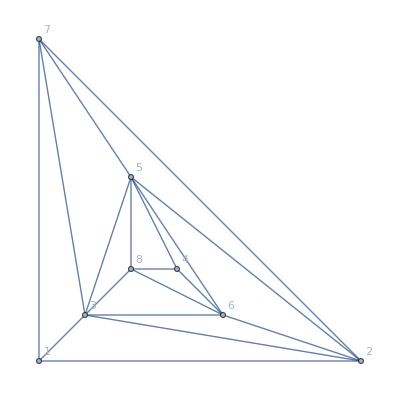

```mathematica
Graph[ReadGrof[10],GraphLayout->"PlanarEmbedding",VertexLabels->"Name"]
```

RGBColor[1, 0, 0]RGBColor[0, 1, 0]RGBColor[0, 0, 1]RGBColor[1, 1, 0]RGBColor[1, 1, 0]RGBColor[1, 0, 0]RGBColor[1, 0, 0]RGBColor[0, 1, 0]RGBColor[1, 1, 0]

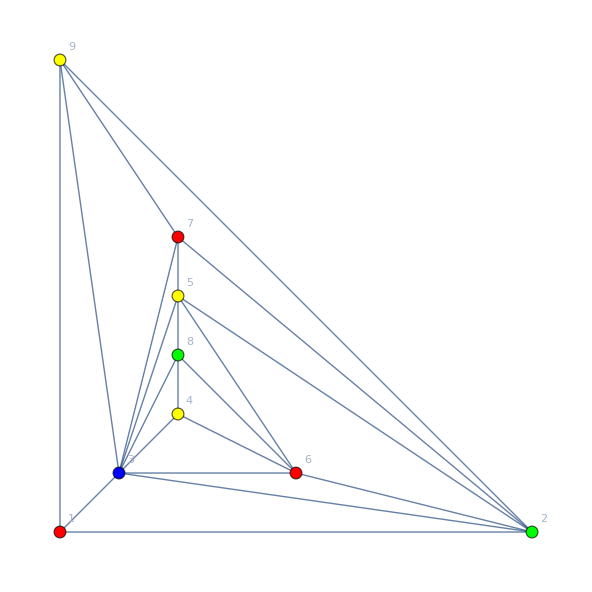

```mathematica
PaintGraph2[ReadGrof[50],"x1==1&&x2==2&&x3==3",VertexLabels->"Name"]
```

```mathematica
Take[deps3,-20]
```

{{58714,364402,{3,{4,3,7,10,5},{3<->5,3<->10},{{3,4,5},{3,5,10},{3,7,10}}}},{58714,364432,{3,{4,5,7,10,3},{3<->5,5<->10},{{3,4,5},{3,5,10},{5,7,10}}}},{58714,364503,{3,{3,5,12,6,4},{4<->5,5<->6},{{3,4,5},{4,5,6},{5,6,12}}}},{58714,364406,{3,{6,3,10,5,4},{3<->4,3<->5},{{3,4,6},{3,4,5},{3,5,10}}}},{58714,364400,{3,{4,3,2,9,6},{3<->6,3<->9},{{3,4,6},{3,6,9},{2,3,9}}}},{58714,393808,{3,{8,5,3,10,7},{5<->7,5<->10},{{5,7,8},{5,7,10},{3,5,10}}}},{58714,373131,{3,{10,5,12,8,7},{5<->7,5<->8},{{5,7,10},{5,7,8},{5,8,12}}}},{58715,394827,{3,{2,1,3,10,5},{1<->5,1<->10},{{1,2,5},{1,5,10},{1,3,10}}}},{58715,394514,{3,{2,5,7,10,1},{1<->5,5<->10},{{1,2,5},{1,5,10},{5,7,10}}}},{58716,394827,{3,{2,5,4,3,1},{1<->5,3<->5},{{1,2,5},{1,3,5},{3,4,5}}}},{58716,398406,{3,{1,2,3,13,5},{2<->5,2<->13},{{1,2,5},{2,5,13},{2,3,13}}}},{58716,395242,{3,{1,5,9,13,2},{2<->5,5<->13},{{1,2,5},{2,5,13},{5,9,13}}}},{58716,398050,{3,{3,5,13,2,1},{1<->5,2<->5},{{1,3,5},{1,2,5},{2,5,13}}}},{58716,395284,{3,{9,3,6,10,7},{3<->7,3<->10},{{3,7,9},{3,7,10},{3,6,10}}}},{58716,398420,{3,{9,7,5,10,3},{3<->7,7<->10},{{3,7,9},{3,7,10},{5,7,10}}}},{58716,395243,{3,{7,3,2,13,9},{3<->9,3<->13},{{3,7,9},{3,9,13},{2,3,13}}}},{58716,398427,{3,{3,7,10,5,9},{7<->9,5<->7},{{3,7,9},{5,7,9},{5,7,10}}}},{58716,398413,{3,{3,9,13,5,7},{7<->9,5<->9},{{3,7,9},{5,7,9},{5,9,13}}}},{58716,395251,{3,{10,3,8,12,6},{3<->6,3<->12},{{3,6,10},{3,6,12},{3,8,12}}}},{58716,398408,{3,{3,11,8,5,4},{4<->11,5<->11},{{3,4,11},{4,5,11},{5,8,11}}}}}

RGBColor[1, 0, 0]RGBColor[1, 0, 0]RGBColor[1, 1, 0]RGBColor[1, 1, 0]RGBColor[1, 0, 0]RGBColor[0, 1, 0]RGBColor[0, 0, 1]RGBColor[1, 1, 0]RGBColor[0, 1, 0]RGBColor[1, 0, 0]RGBColor[1, 1, 0]RGBColor[0, 0, 1]RGBColor[1, 1, 0]

RGBColor[1, 0, 0]RGBColor[1, 0, 0]RGBColor[0, 0, 1]RGBColor[0, 0, 1]RGBColor[0, 0, 1]RGBColor[0, 1, 0]RGBColor[0, 0, 1]RGBColor[1, 0, 0]RGBColor[0, 1, 0]RGBColor[1, 1, 0]RGBColor[1, 1, 0]RGBColor[1, 0, 0]RGBColor[1, 0, 0]

RGBColor[1, 0, 0]RGBColor[1, 0, 0]RGBColor[1, 0, 0]RGBColor[1, 0, 0]RGBColor[1, 0, 0]RGBColor[0, 1, 0]RGBColor[0, 0, 1]RGBColor[1, 0, 0]RGBColor[0, 1, 0]RGBColor[1, 1, 0]RGBColor[1, 1, 0]RGBColor[0, 0, 1]RGBColor[1, 0, 0]

RGBColor[1, 0, 0]RGBColor[0, 1, 0]RGBColor[1, 0, 0]RGBColor[0, 1, 0]RGBColor[1, 0, 0]RGBColor[0, 1, 0]RGBColor[0, 0, 1]RGBColor[0, 1, 0]RGBColor[1, 0, 0]RGBColor[1, 1, 0]RGBColor[1, 1, 0]RGBColor[0, 0, 1]RGBColor[1, 0, 0]

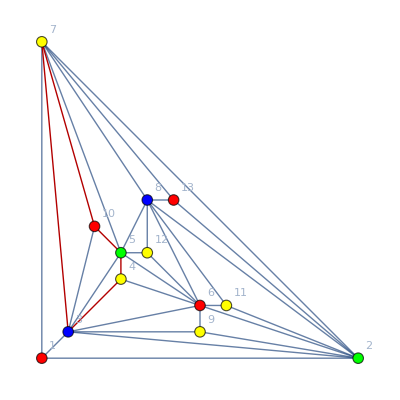
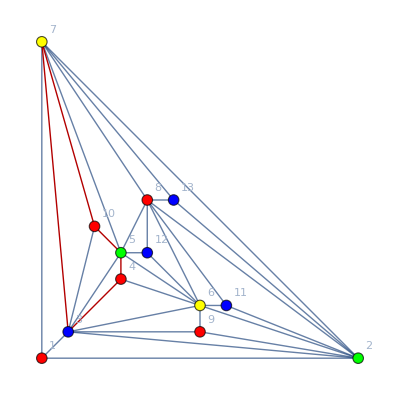
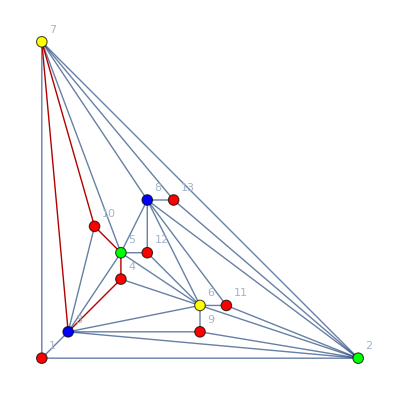
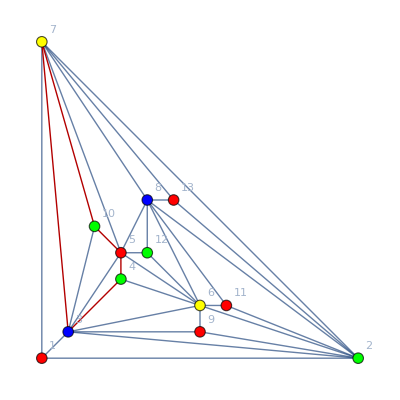

```mathematica
PaintGraph2[ReadGrof[58714],"x1==1&&x2==2&&x3==3",GraphHighlight->Rule3Cycle[{4,3,7,10,5}],ImageSize->400, VertexLabels->"Name", VertexSize->Large]
```

RGBColor[0, 1, 0]RGBColor[1, 1, 0]RGBColor[0, 0, 1]RGBColor[0, 1, 0]RGBColor[1, 0, 0]RGBColor[1, 0, 0]RGBColor[1, 1, 0]RGBColor[1, 0, 0]RGBColor[0, 0, 1]RGBColor[0, 1, 0]RGBColor[0, 0, 1]RGBColor[1, 1, 0]

RGBColor[0, 1, 0]RGBColor[1, 0, 0]RGBColor[1, 1, 0]RGBColor[1, 1, 0]RGBColor[1, 0, 0]RGBColor[1, 1, 0]RGBColor[0, 1, 0]RGBColor[1, 0, 0]RGBColor[0, 0, 1]RGBColor[0, 1, 0]RGBColor[0, 0, 1]RGBColor[0, 0, 1]

RGBColor[0, 1, 0]RGBColor[1, 0, 0]RGBColor[0, 0, 1]RGBColor[1, 1, 0]RGBColor[1, 0, 0]RGBColor[1, 1, 0]RGBColor[0, 1, 0]RGBColor[1, 1, 0]RGBColor[0, 0, 1]RGBColor[0, 1, 0]RGBColor[0, 0, 1]RGBColor[1, 0, 0]

RGBColor[0, 1, 0]RGBColor[1, 0, 0]RGBColor[1, 1, 0]RGBColor[0, 1, 0]RGBColor[1, 0, 0]RGBColor[1, 1, 0]RGBColor[0, 0, 1]RGBColor[1, 0, 0]RGBColor[1, 1, 0]RGBColor[0, 1, 0]RGBColor[0, 0, 1]RGBColor[0, 0, 1]

RGBColor[0, 0, 1]RGBColor[1, 1, 0]RGBColor[0, 0, 1]RGBColor[0, 1, 0]RGBColor[1, 0, 0]RGBColor[1, 0, 0]RGBColor[1, 1, 0]RGBColor[0, 1, 0]RGBColor[1, 0, 0]RGBColor[0, 1, 0]RGBColor[0, 0, 1]RGBColor[1, 1, 0]

RGBColor[0, 0, 1]RGBColor[0, 1, 0]RGBColor[0, 0, 1]RGBColor[1, 1, 0]RGBColor[1, 0, 0]RGBColor[1, 1, 0]RGBColor[0, 1, 0]RGBColor[1, 1, 0]RGBColor[1, 0, 0]RGBColor[0, 1, 0]RGBColor[0, 0, 1]RGBColor[1, 0, 0]

RGBColor[0, 0, 1]RGBColor[0, 1, 0]RGBColor[1, 1, 0]RGBColor[1, 1, 0]RGBColor[1, 0, 0]RGBColor[1, 1, 0]RGBColor[0, 0, 1]RGBColor[0, 1, 0]RGBColor[1, 0, 0]RGBColor[0, 1, 0]RGBColor[0, 0, 1]RGBColor[1, 0, 0]

RGBColor[0, 0, 1]RGBColor[1, 0, 0]RGBColor[1, 1, 0]RGBColor[0, 1, 0]RGBColor[1, 0, 0]RGBColor[1, 1, 0]RGBColor[0, 0, 1]RGBColor[0, 1, 0]RGBColor[1, 1, 0]RGBColor[0, 1, 0]RGBColor[0, 0, 1]RGBColor[1, 0, 0]

RGBColor[1, 1, 0]RGBColor[0, 1, 0]RGBColor[1, 1, 0]RGBColor[1, 1, 0]RGBColor[1, 0, 0]RGBColor[1, 0, 0]RGBColor[0, 1, 0]RGBColor[1, 0, 0]RGBColor[0, 0, 1]RGBColor[0, 1, 0]RGBColor[0, 0, 1]RGBColor[0, 0, 1]

RGBColor[1, 1, 0]RGBColor[0, 1, 0]RGBColor[1, 1, 0]RGBColor[1, 1, 0]RGBColor[1, 0, 0]RGBColor[1, 0, 0]RGBColor[0, 0, 1]RGBColor[0, 1, 0]RGBColor[1, 0, 0]RGBColor[0, 1, 0]RGBColor[0, 0, 1]RGBColor[0, 0, 1]

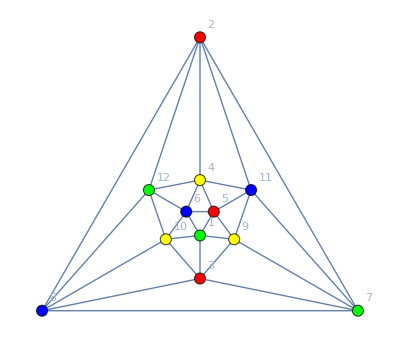
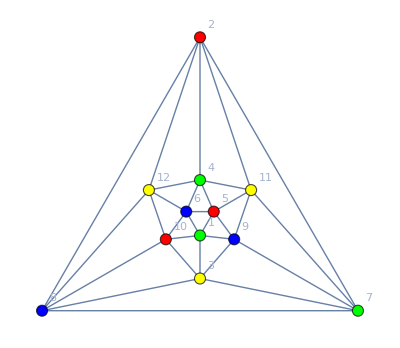
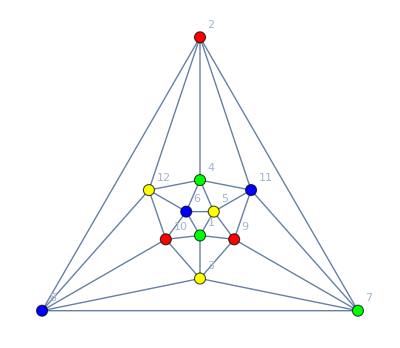
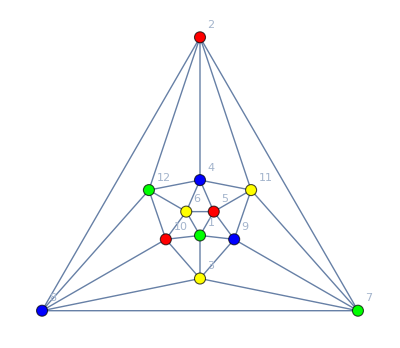
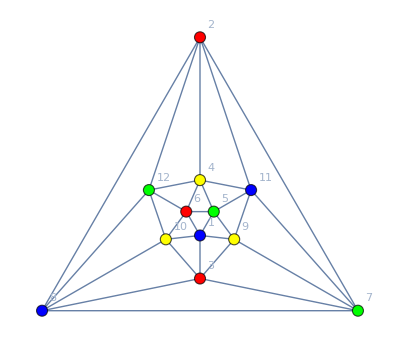
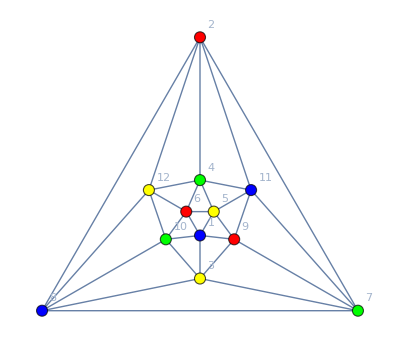
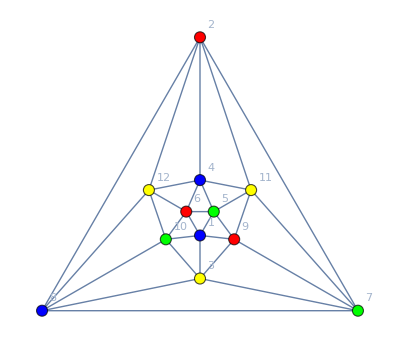
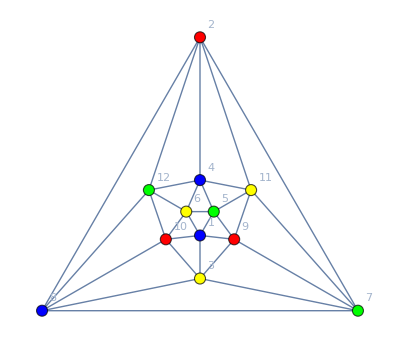

```mathematica
PaintGraph2[GraphData["IcosahedralGraph"],"x2==1&&x7==2&&x8==3",ImageSize->400, VertexLabels->"Name", VertexSize->Large]
```

```mathematica
PlanarGraphQ[GraphData["DodecahedralGraph"]]
```

True

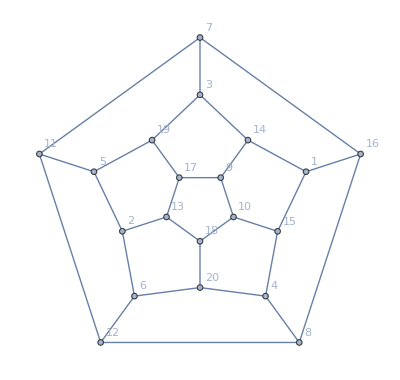

```mathematica
Graph[GraphData["DodecahedralGraph"],VertexLabels->"Name"]
```

```mathematica
PaintGraph2[GraphData["DodecahedralGraph"],"x11==1&&x7==2&&x16==3",ImageSize->400, VertexLabels->"Name", VertexSize->Large]
```

$Aborted